## Computing for Mathematical Physics 2022/23

# Homework 8

# Mark for homework 8: /40 (to be competed by your marker)

# Feedback from marker: (to be competed by your marker)

# Give your answers in the code cells marked (* Enter your solution here *)

Double click the vertical braces on the RHS of each of the three question headings to open and view them.

1. The shooting method. [20 marks]

It may help to quickly refresh your memory regarding the shooting method, revisiting the last question in this week’s class exercises and/or the last section of this week’s lecture notebook.

a) Code the following differential equation in Mathematica, assigning it the label q1DifferentialEquation: 

• eq. 1.1 :   (d^2 y)/(d t^2)  + y^3= 7 Cos[5 t] ,

Obtain a numerical solution of eq. 1.1 over the range -1 < t < 10, providing the boundary conditions  y[-1]=0 and y[10]=0 to NDSolve, with AccuracyGoal→8 and PrecisionGoal→16. Note: we are not employing the shooting method here in part a) yet, but rather supplying boundary conditions y[-1]=0 and y[10]=0 directly to NDSolve instead. Plot the resulting solution for y(t) for -1 < t < 10.
[6 marks]

y[t]^3+y''[t]==7 Cos[5 t]

{{y[t]→InterpolatingFunction[…][t]}}

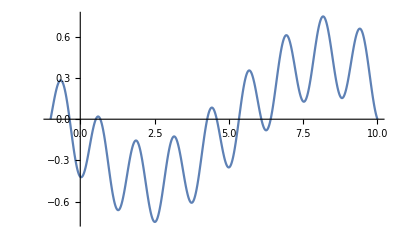

```mathematica
(* Enter code in a new cell immediately below this one. *)
q1DifferentialEquation=D[y[t],{t,2}]+y[t]^3==7Cos[5t]
q1NumericDiffSol=NDSolve[{q1DifferentialEquation, y[-1]==0, y[10]==0}, y[t], {t,-1,10}, AccuracyGoal->8, PrecisionGoal->16]
Plot[y[t]/.q1NumericDiffSol, {t,-1,10}]
```

b) NDSolve, as used in part a), finds just one of many possible solutions to eq. 1.1. The function in the next input cell, q1Solver[slopeGuess_], is adapted from the answer to Q3 b) in week 8’s in-class exercise on the shooting method: it returns a numerical solution for eq. 1.1 with boundary conditions y[-1]=0 and y’[-1]=slopeGuess. Analogous to Q3 c) in week 8’s in-class exercise, define a function, yAttEquals10[slopeGuess_?NumericQ], returning the value of the y[t] solution output by q1Solver[slopeGuess][[1]] at t=10. Use yAttEquals10 to plot the values of y[10] vs y’[-1] when solving eq. 1.1 with the boundary value y[-1]=0, and y’[-1] values between 0 and 1.
[4 marks]

```mathematica
q1Solver[slopeGuess_]:=
NDSolve[
{
(* Differential equation that we need to solve *)
q1DifferentialEquation,
(* Boundary condition y[-1]=0 from the question *)
y[-1]==0,
(* Corresponding boundary condition for y'[t] at *)
(* t = -1 which we set to the slopeGuess value   *)
(* passed to q3Solver as an input.               *)
y'[-1]==slopeGuess
},
(* Specify the function we want a solution for. *)
y,
(* Independent variable and the associated range *)
(* over which we seek a numerical solution.      *)
{t,-1,10}
]
```

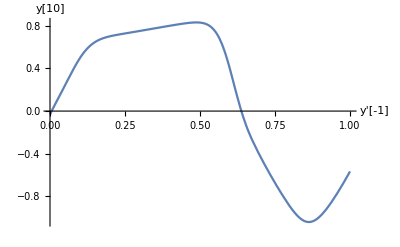

```mathematica
(* Enter code in a new cell immediately below this one. *)
yAttEquals10[slopeGuess_?NumericQ]:=y[t]/.(q1Solver[slopeGuess][[1]])/.t->10
Plot[yAttEquals10[slope], {slope, 0,1}, AxesLabel->{"y'[-1]","y[10]"}]
```

c) Guided by the plot from part b), use FindRoot and yAttEquals10 to precisely determine the two values of y’[-1], between 0 and 1, corresponding to solutions of eq. 1.1 that satisfy  y[-1]=0 and y[10]=0. Assign the solution corresponding to the smallest y’[-1] value to the variable slopeSolution1. Assign the solution corresponding to the larger y’[-1] value to the variable slopeSolution2.
[4 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
slopeSolution1=x/.FindRoot[yAttEquals10[x]==0,{x,0}]
slopeSolution2=x/.FindRoot[yAttEquals10[x]==0,{x,0.6}]
```

0.00550158

0.63786

d) Solve eq. 1.1 using the boundary conditions y[-1]=0 and  y’[-1]=slopeSolution1, over the range -1 < t < 10, assigning the solution to the symbol q1DSolution1. Solve eq. 1.1 using the boundary conditions y[-1]=0 and  y’[-1]=slopeSolution2, over the range -1 < t < 10, assigning the solution to the symbol q1DSolution2. Plot these two solutions on the same graph, with due care given to its presentation. 
[6 marks]

{{y[t]→InterpolatingFunction[…][t]}}

{{y[t]→InterpolatingFunction[…][t]}}

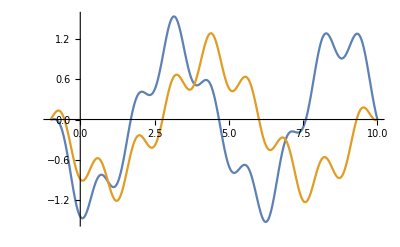

```mathematica
(* Enter code in a new cell immediately below this one. *)
q1DSolution1 = NDSolve[{q1DifferentialEquation, y[-1]==0, y'[-1]==slopeSolution1}, y[t], {t,-1,10}, AccuracyGoal->8, PrecisionGoal->16]
q1DSolution2 = NDSolve[{q1DifferentialEquation, y[-1]==0, y'[-1]==slopeSolution2}, y[t], {t,-1,10}, AccuracyGoal->8, PrecisionGoal->16]
Plot[{y[t]/.q1DSolution1,y[t]/.q1DSolution2}, {t,-1,10}]
```

2. Numerical solving equations of motion. [20 marks]

Two particles, each of unit mass in some system of units, move along the x axis and are joined by a spring of natural length L=1 and spring constant k=5. The particles are initially released from rest with one particle at x=0.1 and the other at x=0.9.

```mathematica
Clear["Global`*"]
```

a) Code the masses of the two particles as m1=1, m2=1. Code the natural length of the spring as L=1, and the spring constant as k=5. Similarly, declare the maximum time period over which we will consider the evolution as tMax=100.

N.B. From part b) onward, the variables, m1, m2, L, k, and tMax should be used, whenever appropriate, to refer to those physical quantities in the code; instead of explicitly entering (hard-wiring) their corresponding numerical values in formulae. 

[0 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
m1=1;
m2=1;
L=1;
k=5;
tMax=100;
```

b) Set up and solve, numerically, the equations of motion for the particles, from time t=0 up to t=tMax=100. Plot the positions of the two particles as a function of time, on the same graph.
[9 marks]

x1''[t]==5 (-1-x1[t]+x2[t])

x2''[t]==5 (1+x1[t]-x2[t])

{{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t]}}

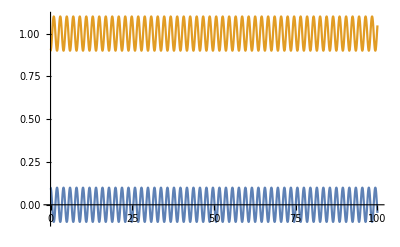

```mathematica
(* Enter code in a new cell immediately below this one. *)
q2DiffEq1 = m1 D[x1[t], {t,2}]==k(x2[t]-x1[t]-L)
q2DiffEq2 = m2 D[x2[t], {t,2}]==k(x1[t]-x2[t]+L)
q2DiffNumSols=NDSolve[{q2DiffEq1,q2DiffEq2, x1[0]==0.1,x2[0]==0.9, x1'[0]==0,x2'[0]==0}, {x1[t],x2[t]},{t,0,tMax}]
Plot[{x1[t]/.q2DiffNumSols,x2[t]/.q2DiffNumSols}, {t,0,tMax}]
```

c) The kinetic energy of a single particle of mass m moving with velocity (d x)/(d t) is 1/2 m ((d x)/(d t))^2. The elastic energy in a spring of natural length L, and spring constant k, when its length is d, is 1/2(k(L-d))^2. Using this information, plot the total energy in the system as a function of time.
[5 marks]

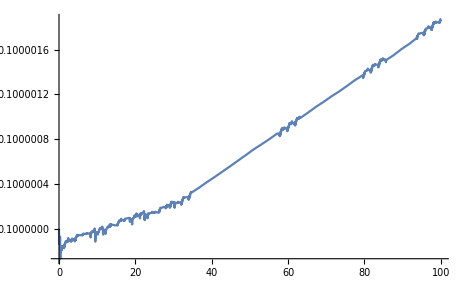

```mathematica
(* Enter code in a new cell immediately below this one. *)
x1[t]=x1[t]/.q2DiffNumSols;
x2[t]=x2[t]/.q2DiffNumSols;
keTotal[t_] = 1/2*m1*(D[x1[t],t])^2 + 1/2*m2*(D[x2[t],t])^2;
epeTotal[t_] = 1/2*k* (L-(x2[t]-x1[t]))^2;
eTotal[t_]=keTotal[t]+epeTotal[t];
Plot[eTotal[t],{t,0,tMax}]
```

d) Repeat b) and c) for the case in which the particles are released from rest at x=0.4 and x=0.6. Plot the positions of the two particles as a function of time, on the same graph. Also, separately, plot the total energy in the system as a function of time, choosing the range displayed so as to show any trends. Comment briefly on the latter plot in a text cell.
[6 marks]

{{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t]}}

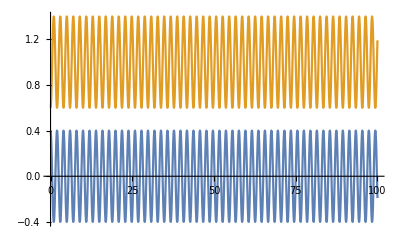

-Graphics-

```mathematica
(* Enter code in a new cell immediately below this one. *)
Clear[x1,x2]
q2DiffNumSols2=NDSolve[{q2DiffEq1,q2DiffEq2, x1[0]==0.4,x2[0]==0.6, x1'[0]==0,x2'[0]==0}, {x1[t],x2[t]},{t,0,tMax}]
Plot[{x1[t]/.q2DiffNumSols2,x2[t]/.q2DiffNumSols2}, {t,0,tMax}]
x1[t]=x1[t]/.q2DiffNumSols2;
x2[t]=x2[t]/.q2DiffNumSols2;
keTotal[t_] = 1/2*m1*(D[x1[t],t])^2 + 1/2*m2*(D[x2[t],t])^2;
epeTotal[t_] = 1/2*k* (L-(x2[t]-x1[t]))^2;
eTotal[t_]=keTotal[t]+epeTotal[t];
Plot[eTotal[t],{t,0,10*tMax}]
```

The graph illustrating the total energy of the system, derived from the numerical differential equation solution, shows an exponential growth. This shows that the numerical solution would not be suitable past the given time of tMax=100, as the total energy should be constant for the system, thus this violates conservation of energy.

Total marks available: 40

Solutions are due by 1200 noon on Thursday March 16th here:  allow time for uploading on moodle.

A 10% mark deduction will be made (4 marks) if the template isn’t used.

Name your solution notebook file in the format WK8_HMWK_<Initials>_<Family Name>.nb, e.g. WK8_HMWK_K_Hamilton.nb

Make a backup copy of your solutions.

Delete all cell evaluation output by selecting Cell → Delete All Output from the drop-down menus at the top of the screen, then save and upload that file to Moodle.

The first thing your marker will do when they receive your notebook is to evaluate all of it, to regenerate the output, by clicking Evaluation → Evaluate Notebook from the drop-down menus at the top of the screen. It is your responsibility to check that carrying out this process will produce the output you intend it to, before you upload your work.

K. Hamilton
15:35 21 Feb 2023